Matrix Inversion Polynomial, mostly from Gilyen et al QSVT tome, but using a form of the rectangle function approximation from Low’s thesis

```mathematica
ntemp[β_, ϵ_]:=Ceiling[Sqrt[2*Log[4/ϵ]]*Sqrt[Ceiling[Max[β*ⅇ^2, Log[2/ϵ]]]]];
ferftemp[x_, k_, n_]:=2*k*ⅇ^(-k^2/2)/Sqrt[π]*(Sum[(-1)^j*(BesselI[j, k^2/2]+BesselI[j+1, k^2/2])/(2*j+1)*ChebyshevT[2*j+1, x], {j, 0, (n-3)/2}]+(-1)^((n-1)/2)*BesselI[(n-1)/2, k^2/2]/n*ChebyshevT[n, x]);
ktemp[κ_, ϵ_]:=Sqrt[2]/κ*Sqrt[Log[8/π/ϵ^2]];
```

```mathematica
fl16[x_, a_,κ_, ϵ_]:=ferftemp[(x-a)/2, 2*ktemp[κ, ϵ],  2*ntemp[2*ktemp[κ, ϵ]^2,Sqrt[π]* ϵ/16/ktemp[κ, ϵ]]+1];
```

```mathematica
fgslw29rect[x_, t_, δ_, ϵ_]:=(fl16[x,-t-δ/4 ,δ/2, ϵ]-fl16[x, t+δ/4,δ/2, ϵ])/2 ;
```

```mathematica
ka1=2;
e1=10^(-4);
```

In the the above approx, t is half the width of the approx. Problem is that the range of the validity is centered for each sign function, see plot below

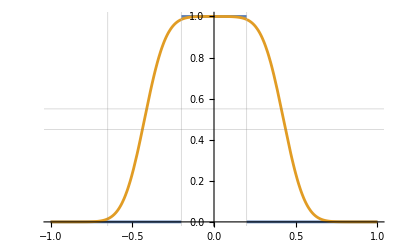

```mathematica
(*Plot[{(-Sign[x-a1]+Sign[x+a1])/2, (fl16[x,-a1-delt1/4 ,delt1/2, e1/3]-fl16[x, a1+delt1/4 ,delt1/2,e1/3])/2}, {x,-1, 1}, PlotRange->Full, GridLines->{{-a1-delt1/2,-a1, a1, a1+delt1}, {e1, 1-e1, 1+e1}}]*)
```

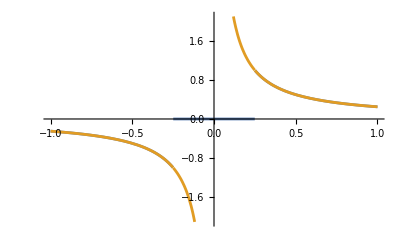

```mathematica
Plot[{(1-Sign[x+1/ka1/2]/2+Sign[x-1/ka1/2]/2)/x/ka1/2, 1/x/ka1/2}, {x, -1, 1}, GridLines->{{-1/ka1,-1/2/ka1,1/2/ka1, 1/ka1}, {-1,0,1}}]
```

```mathematica
b[κ_, ϵ_]:=Ceiling[κ^2*Log[κ/ϵ]];
j0[κ_, ϵ_]:=Ceiling[Sqrt[b[κ, ϵ]*Log[4*b[κ, ϵ]/ϵ]]];
finv[x_, κ_, ϵ_]:=4*Sum[(-1)^j/2^(2*b[κ, ϵ]) *Sum[Binomial[2*b[κ, ϵ], b[κ, ϵ]+i], {i, j+1, b[κ, ϵ]}]*ChebyshevT[2*j+1, x], {j, 0, j0[κ, ϵ]}];
```

```mathematica
cond=2;
```

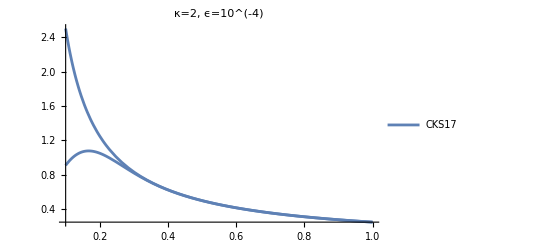

```mathematica
Plot[{finv[x,cond, e1], 1/x}/2/cond, {x, 0.1, 1}, PlotLegends->{"CKS17", "1/x"}, PlotLabel->"κ=2, ϵ=10^(-4)", GridLines->{{1/cond/2, 1/cond}, {0,1, 1+e1}}, PlotRange->Full]
```

```mathematica
fMI[x_, κ_, ϵ_]:=(1-fgslw29rect[x, 1/2/κ, 1/κ, Min[ϵ, κ/2/j0[κ, ϵ]]])*finv[x, κ, ϵ]/2/κ;
```

```mathematica
e1=10^(-1);
cond=5
```

5

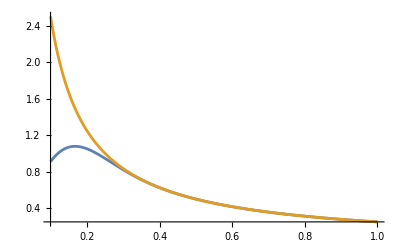

```mathematica
(*Plot[{fMI[x, cond, e1], 1/x/cond/2}, {x, 0.1, 1}, PlotRange->Full, GridLines->{{1/cond/2, 1/cond}, {1, 1+e1}}]*)
```

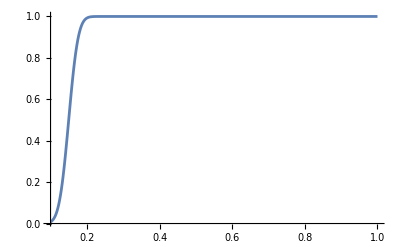

```mathematica
Plot[1-fgslw29rect[x, 1/2/cond, 1/cond, Min[e1, cond/2/j0[cond, e1]]], {x, 0.1, 1}, PlotRange->Full, GridLines->{{1/cond/2, 1/cond}, {1, 1+e1}}]
```

This means that what happened above was the rect( ) function returned zero...this happens bc of some stupidity in the size of the coefficients. Try a much worse epsilon

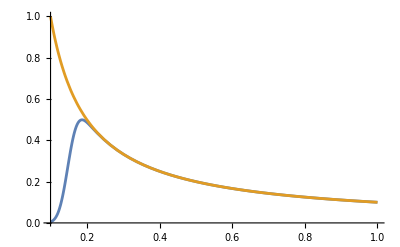

```mathematica
Plot[{fMI[x, cond, e1], 1/x/cond/2}, {x, 0.1, 1}, PlotRange->Full, GridLines->{{1/cond/2, 1/cond}, {1, 1+e1}}]
```

bit worried about the <1/2/κ range bc the approx is supposed to be valid? (ig the 1/x function could change that??) Actually nvm epsilon is really big here so that’s probably why it looks strange. double check that range is within P_{inv}\epsilon later if necessary

```mathematica
Simplify[fgslw29rect[x, 1/2/cond, 1/cond, Min[e1, cond/2/j0[cond, e1]]]]
F2:=Simplify[fMI[x, cond, e1]/.x->(z+z^(-1))/2];
```

```mathematica
nMI[κ_, ϵ_]:=2*j0[κ, ϵ]+1+2*ntemp[2*ktemp[1/κ/2, Min[ϵ, κ/2/j0[κ, ϵ]]]^2,Sqrt[π]* Min[ϵ, κ/2/j0[κ, ϵ]]/16/ktemp[1/κ/2, Min[ϵ, κ/2/j0[κ, ϵ]]]]+1
```

```mathematica
nMI[cond, e1]
```

1210

```mathematica
n1=nMI[cond, e1]
```

1210

```mathematica
LaurentList=N[CoefficientList[Simplify[z^n1*F2], {z}]]
```

{1.13634×10^-20,0.,-3.91629×10^-20,0.,1.32132×10^-19,0.,-4.36529×10^-19,0.,1.41253×10^-18,0.,-4.4778×10^-18,0.,1.39094×10^-17,0.,-4.2347×10^-17,0.,1.26387×10^-16,0.,-3.69855×10^-16,0.,1.06144×10^-15,0.,-2.98802×10^-15,0.,8.25217×10^-15,0.,-2.2363×10^-14,0.,5.94765×10^-14,0.,-1.55269×10^-13,0.,3.97945×10^-13,0.,-1.00144×10^-12,0.,2.47491×10^-12,0.,-6.00746×10^-12,0.,1.43246×10^-11,0.,-3.3558×10^-11,0.,7.72486×10^-11,0.,-1.74753×10^-10,0.,3.88559×10^-10,0.,-8.49259×10^-10,0.,1.82486×10^-9,0.,-3.85547×10^-9,0.,8.01005×10^-9,0.,-1.63664×10^-8,0.,3.28914×10^-8,0.,-6.50232×10^-8,0.,1.26462×10^-7,0.,-2.41994×10^-7,0.,4.55666×10^-7,0.,-8.44367×10^-7,0.,1.53994×10^-6,0.,-2.76443×10^-6,0.,4.8852×10^-6,0.,-8.49917×10^-6,0.,0.000014559,0.,-0.0000245576,0.,0.000040793,0.,-0.0000667379,0.,0.000107544,0.,-0.000170716,0.,0.000266977,0.,-0.000411369,0.,0.000624584,0.,-0.000934535,0.,0.00137813,0.,-0.00200321,0.,0.00287042,0.,-0.0040551,0.,0.00564865,0.,-0.00775941,0.,0.0105126,0.,-0.014049,0.,0.0185223,0.,-0.0240951,0.,0.0309323,0.,-0.0391939,0.,0.0490259,0.,-0.0605502,0.,0.0738548,0.,-0.0889834,0.,0.105927,0.,-0.12462,0.,0.144931,0.,-0.16667,0.,0.189589,0.,-0.213389,0.,0.237735,0.,0.237735,0.,-0.213389,0.,0.189589,0.,-0.16667,0.,0.144931,0.,-0.12462,0.,0.105927,0.,-0.0889834,0.,0.0738548,0.,-0.0605502,0.,0.0490259,0.,-0.0391939,0.,0.0309323,0.,-0.0240951,0.,0.0185223,0.,-0.014049,0.,0.0105126,0.,-0.00775941,0.,0.00564865,0.,-0.0040551,0.,0.00287042,0.,-0.00200321,0.,0.00137813,0.,-0.000934535,0.,0.000624584,0.,-0.000411369,0.,0.000266977,0.,-0.000170716,0.,0.000107544,0.,-0.0000667379,0.,0.000040793,0.,-0.0000245576,0.,0.000014559,0.,-8.49917×10^-6,0.,4.8852×10^-6,0.,-2.76443×10^-6,0.,1.53994×10^-6,0.,-8.44367×10^-7,0.,4.55666×10^-7,0.,-2.41994×10^-7,0.,1.26462×10^-7,0.,-6.50232×10^-8,0.,3.28914×10^-8,0.,-1.63664×10^-8,0.,8.01005×10^-9,0.,-3.85547×10^-9,0.,1.82486×10^-9,0.,-8.49259×10^-10,0.,3.88559×10^-10,0.,-1.74753×10^-10,0.,7.72486×10^-11,0.,-3.3558×10^-11,0.,1.43246×10^-11,0.,-6.00746×10^-12,0.,2.47491×10^-12,0.,-1.00144×10^-12,0.,3.97945×10^-13,0.,-1.55269×10^-13,0.,5.94765×10^-14,0.,-2.2363×10^-14,0.,8.25217×10^-15,0.,-2.98802×10^-15,0.,1.06144×10^-15,0.,-3.69855×10^-16,0.,1.26387×10^-16,0.,-4.2347×10^-17,0.,1.39094×10^-17,0.,-4.4778×10^-18,0.,1.41253×10^-18,0.,-4.36529×10^-19,0.,1.32132×10^-19,0.,-3.91629×10^-20,0.,1.13634×10^-20}

```mathematica
A=Partition[LaurentList,2,2,1,{}]~Flatten~{2};
LeadingList=Riffle[A[[1]], 0, 2]
NonleadingList=Riffle[A[[2]], 0, {1, 2*n1+1, 2}]
```

{1.13634×10^-20,0,-3.91629×10^-20,0,1.32132×10^-19,0,-4.36529×10^-19,0,1.41253×10^-18,0,-4.4778×10^-18,0,1.39094×10^-17,0,-4.2347×10^-17,0,1.26387×10^-16,0,-3.69855×10^-16,0,1.06144×10^-15,0,-2.98802×10^-15,0,8.25217×10^-15,0,-2.2363×10^-14,0,5.94765×10^-14,0,-1.55269×10^-13,0,3.97945×10^-13,0,-1.00144×10^-12,0,2.47491×10^-12,0,-6.00746×10^-12,0,1.43246×10^-11,0,-3.3558×10^-11,0,7.72486×10^-11,0,-1.74753×10^-10,0,3.88559×10^-10,0,-8.49259×10^-10,0,1.82486×10^-9,0,-3.85547×10^-9,0,8.01005×10^-9,0,-1.63664×10^-8,0,3.28914×10^-8,0,-6.50232×10^-8,0,1.26462×10^-7,0,-2.41994×10^-7,0,4.55666×10^-7,0,-8.44367×10^-7,0,1.53994×10^-6,0,-2.76443×10^-6,0,4.8852×10^-6,0,-8.49917×10^-6,0,0.000014559,0,-0.0000245576,0,0.000040793,0,-0.0000667379,0,0.000107544,0,-0.000170716,0,0.000266977,0,-0.000411369,0,0.000624584,0,-0.000934535,0,0.00137813,0,-0.00200321,0,0.00287042,0,-0.0040551,0,0.00564865,0,-0.00775941,0,0.0105126,0,-0.014049,0,0.0185223,0,-0.0240951,0,0.0309323,0,-0.0391939,0,0.0490259,0,-0.0605502,0,0.0738548,0,-0.0889834,0,0.105927,0,-0.12462,0,0.144931,0,-0.16667,0,0.189589,0,-0.213389,0,0.237735,0,0.237735,0,-0.213389,0,0.189589,0,-0.16667,0,0.144931,0,-0.12462,0,0.105927,0,-0.0889834,0,0.0738548,0,-0.0605502,0,0.0490259,0,-0.0391939,0,0.0309323,0,-0.0240951,0,0.0185223,0,-0.014049,0,0.0105126,0,-0.00775941,0,0.00564865,0,-0.0040551,0,0.00287042,0,-0.00200321,0,0.00137813,0,-0.000934535,0,0.000624584,0,-0.000411369,0,0.000266977,0,-0.000170716,0,0.000107544,0,-0.0000667379,0,0.000040793,0,-0.0000245576,0,0.000014559,0,-8.49917×10^-6,0,4.8852×10^-6,0,-2.76443×10^-6,0,1.53994×10^-6,0,-8.44367×10^-7,0,4.55666×10^-7,0,-2.41994×10^-7,0,1.26462×10^-7,0,-6.50232×10^-8,0,3.28914×10^-8,0,-1.63664×10^-8,0,8.01005×10^-9,0,-3.85547×10^-9,0,1.82486×10^-9,0,-8.49259×10^-10,0,3.88559×10^-10,0,-1.74753×10^-10,0,7.72486×10^-11,0,-3.3558×10^-11,0,1.43246×10^-11,0,-6.00746×10^-12,0,2.47491×10^-12,0,-1.00144×10^-12,0,3.97945×10^-13,0,-1.55269×10^-13,0,5.94765×10^-14,0,-2.2363×10^-14,0,8.25217×10^-15,0,-2.98802×10^-15,0,1.06144×10^-15,0,-3.69855×10^-16,0,1.26387×10^-16,0,-4.2347×10^-17,0,1.39094×10^-17,0,-4.4778×10^-18,0,1.41253×10^-18,0,-4.36529×10^-19,0,1.32132×10^-19,0,-3.91629×10^-20,0,1.13634×10^-20}

{0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0}

```mathematica
OddList=If[EvenQ[n1]==True, NonleadingList, LeadingList];
EvenList=If[EvenQ[n1]==True, LeadingList, NonleadingList];
```

{1.13634×10^-20,0,-3.91629×10^-20,0,1.32132×10^-19,0,-4.36529×10^-19,0,1.41253×10^-18,0,-4.4778×10^-18,0,1.39094×10^-17,0,-4.2347×10^-17,0,1.26387×10^-16,0,-3.69855×10^-16,0,1.06144×10^-15,0,-2.98802×10^-15,0,8.25217×10^-15,0,-2.2363×10^-14,0,5.94765×10^-14,0,-1.55269×10^-13,0,3.97945×10^-13,0,-1.00144×10^-12,0,2.47491×10^-12,0,-6.00746×10^-12,0,1.43246×10^-11,0,-3.3558×10^-11,0,7.72486×10^-11,0,-1.74753×10^-10,0,3.88559×10^-10,0,-8.49259×10^-10,0,1.82486×10^-9,0,-3.85547×10^-9,0,8.01005×10^-9,0,-1.63664×10^-8,0,3.28914×10^-8,0,-6.50232×10^-8,0,1.26462×10^-7,0,-2.41994×10^-7,0,4.55666×10^-7,0,-8.44367×10^-7,0,1.53994×10^-6,0,-2.76443×10^-6,0,4.8852×10^-6,0,-8.49917×10^-6,0,0.000014559,0,-0.0000245576,0,0.000040793,0,-0.0000667379,0,0.000107544,0,-0.000170716,0,0.000266977,0,-0.000411369,0,0.000624584,0,-0.000934535,0,0.00137813,0,-0.00200321,0,0.00287042,0,-0.0040551,0,0.00564865,0,-0.00775941,0,0.0105126,0,-0.014049,0,0.0185223,0,-0.0240951,0,0.0309323,0,-0.0391939,0,0.0490259,0,-0.0605502,0,0.0738548,0,-0.0889834,0,0.105927,0,-0.12462,0,0.144931,0,-0.16667,0,0.189589,0,-0.213389,0,0.237735,0,0.237735,0,-0.213389,0,0.189589,0,-0.16667,0,0.144931,0,-0.12462,0,0.105927,0,-0.0889834,0,0.0738548,0,-0.0605502,0,0.0490259,0,-0.0391939,0,0.0309323,0,-0.0240951,0,0.0185223,0,-0.014049,0,0.0105126,0,-0.00775941,0,0.00564865,0,-0.0040551,0,0.00287042,0,-0.00200321,0,0.00137813,0,-0.000934535,0,0.000624584,0,-0.000411369,0,0.000266977,0,-0.000170716,0,0.000107544,0,-0.0000667379,0,0.000040793,0,-0.0000245576,0,0.000014559,0,-8.49917×10^-6,0,4.8852×10^-6,0,-2.76443×10^-6,0,1.53994×10^-6,0,-8.44367×10^-7,0,4.55666×10^-7,0,-2.41994×10^-7,0,1.26462×10^-7,0,-6.50232×10^-8,0,3.28914×10^-8,0,-1.63664×10^-8,0,8.01005×10^-9,0,-3.85547×10^-9,0,1.82486×10^-9,0,-8.49259×10^-10,0,3.88559×10^-10,0,-1.74753×10^-10,0,7.72486×10^-11,0,-3.3558×10^-11,0,1.43246×10^-11,0,-6.00746×10^-12,0,2.47491×10^-12,0,-1.00144×10^-12,0,3.97945×10^-13,0,-1.55269×10^-13,0,5.94765×10^-14,0,-2.2363×10^-14,0,8.25217×10^-15,0,-2.98802×10^-15,0,1.06144×10^-15,0,-3.69855×10^-16,0,1.26387×10^-16,0,-4.2347×10^-17,0,1.39094×10^-17,0,-4.4778×10^-18,0,1.41253×10^-18,0,-4.36529×10^-19,0,1.32132×10^-19,0,-3.91629×10^-20,0,1.13634×10^-20}

{0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0}

C:\Users\skelt\Documents\GitHub\QSVT\csv_files\MI_kappa_2_epsi_1_export.csv

```mathematica
Length[OddList]
```

39

```mathematica
Length[EvenList]
```

39

```mathematica
19*2+1
```

39

```mathematica
Column[Table[n1, {i, 2*n1+1}]];
```

```mathematica
T1={N[EvenList]/2, N[OddList]/2,Table[n1, {i, 2*n1+1}]}
```

{{0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.},{-4.48525×10^-6,0.,0.0000346452,0.,-0.000192985,0.,0.000826344,0.,-0.00283198,0.,0.00798933,0.,-0.0189487,0.,0.038432,0.,-0.067657,0.,0.104852,0.,0.104852,0.,-0.067657,0.,0.038432,0.,-0.0189487,0.,0.00798933,0.,-0.00283198,0.,0.000826344,0.,-0.000192985,0.,0.0000346452,0.,-4.48525×10^-6},{19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19,19}}

```mathematica
T1[[2, 19]]
```

0.104852

```mathematica
Dimensions[T1]
```

{3,39}

```mathematica
(*Export["C:\\Users\\skelt\\Documents\\GitHub\\QSVT\\csv_files\\MI_kappa_2_epsi_1.csv",{T1}, "CSV" ]*)
```

C:\Users\skelt\Documents\GitHub\QSVT\csv_files\MI_kappa_2_epsi_1.csv

```mathematica
CList=Prepend[EvenList/2, "C"]
SList=Prepend[OddList/2, "S"]
nList=Prepend[Table[n1, {i, 1, n1*2+1}], "n"]
```

{C,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0,0.,0}

{S,5.68171×10^-21,0,-1.95814×10^-20,0,6.60658×10^-20,0,-2.18265×10^-19,0,7.06267×10^-19,0,-2.2389×10^-18,0,6.95469×10^-18,0,-2.11735×10^-17,0,6.31933×10^-17,0,-1.84927×10^-16,0,5.30722×10^-16,0,-1.49401×10^-15,0,4.12608×10^-15,0,-1.11815×10^-14,0,2.97383×10^-14,0,-7.76347×10^-14,0,1.98972×10^-13,0,-5.0072×10^-13,0,1.23745×10^-12,0,-3.00373×10^-12,0,7.1623×10^-12,0,-1.6779×10^-11,0,3.86243×10^-11,0,-8.73767×10^-11,0,1.94279×10^-10,0,-4.24629×10^-10,0,9.12429×10^-10,0,-1.92773×10^-9,0,4.00502×10^-9,0,-8.18321×10^-9,0,1.64457×10^-8,0,-3.25116×10^-8,0,6.32311×10^-8,0,-1.20997×10^-7,0,2.27833×10^-7,0,-4.22184×10^-7,0,7.69969×10^-7,0,-1.38222×10^-6,0,2.4426×10^-6,0,-4.24959×10^-6,0,7.27948×10^-6,0,-0.0000122788,0,0.0000203965,0,-0.000033369,0,0.0000537722,0,-0.000085358,0,0.000133489,0,-0.000205685,0,0.000312292,0,-0.000467267,0,0.000689067,0,-0.0010016,0,0.00143521,0,-0.00202755,0,0.00282433,0,-0.00387971,0,0.00525629,0,-0.00702448,0,0.00926117,0,-0.0120476,0,0.0154661,0,-0.0195969,0,0.0245129,0,-0.0302751,0,0.0369274,0,-0.0444917,0,0.0529637,0,-0.0623098,0,0.0724654,0,-0.083335,0,0.0947945,0,-0.106695,0,0.118868,0,0.118868,0,-0.106695,0,0.0947945,0,-0.083335,0,0.0724654,0,-0.0623098,0,0.0529637,0,-0.0444917,0,0.0369274,0,-0.0302751,0,0.0245129,0,-0.0195969,0,0.0154661,0,-0.0120476,0,0.00926117,0,-0.00702448,0,0.00525629,0,-0.00387971,0,0.00282433,0,-0.00202755,0,0.00143521,0,-0.0010016,0,0.000689067,0,-0.000467267,0,0.000312292,0,-0.000205685,0,0.000133489,0,-0.000085358,0,0.0000537722,0,-0.000033369,0,0.0000203965,0,-0.0000122788,0,7.27948×10^-6,0,-4.24959×10^-6,0,2.4426×10^-6,0,-1.38222×10^-6,0,7.69969×10^-7,0,-4.22184×10^-7,0,2.27833×10^-7,0,-1.20997×10^-7,0,6.32311×10^-8,0,-3.25116×10^-8,0,1.64457×10^-8,0,-8.18321×10^-9,0,4.00502×10^-9,0,-1.92773×10^-9,0,9.12429×10^-10,0,-4.24629×10^-10,0,1.94279×10^-10,0,-8.73767×10^-11,0,3.86243×10^-11,0,-1.6779×10^-11,0,7.1623×10^-12,0,-3.00373×10^-12,0,1.23745×10^-12,0,-5.0072×10^-13,0,1.98972×10^-13,0,-7.76347×10^-14,0,2.97383×10^-14,0,-1.11815×10^-14,0,4.12608×10^-15,0,-1.49401×10^-15,0,5.30722×10^-16,0,-1.84927×10^-16,0,6.31933×10^-17,0,-2.11735×10^-17,0,6.95469×10^-18,0,-2.2389×10^-18,0,7.06267×10^-19,0,-2.18265×10^-19,0,6.60658×10^-20,0,-1.95814×10^-20,0,5.68171×10^-21}

{n,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145,145}

```mathematica
Export["C:\\Users\\skelt\\Documents\\GitHub\\QSVT\\csv_files\\MI_kappa_2_epsi_14.csv",Transpose[{CList, SList, nList}], "CSV" ]
```

C:\Users\skelt\Documents\GitHub\QSVT\csv_files\MI_kappa_2_epsi_14.csv

```mathematica
"C:\\Users\\skelt\\Documents\\GitHub\\QSVT\\csv_files\\MI_kappa_2_epsi_14.csv"
```